## BSF History

```mathematica
genomes=ToExpression@StringSplit[Import["~/java/exp/GPAT_K/run_001_010_O_GENOMES_MATH.txt"],"\n"];
```

Finds the genome id of the BSF. Warning it searches only the last generation!

```mathematica
Flatten[{{a,{b,e}},{c,{d,f}}},1]
```

{a,{b,e},c,{d,f}}

```mathematica
findBSFId[genomes_]:=Sort[Flatten[genomes,1],#1⟦4⟧>#2⟦4⟧&]⟦1,1⟧
```

```mathematica
findBSFId[genomes]
```

998633

```mathematica
traceBackIds[parentId_Integer,genomes_]:=
Module[{p,n,i,l={}},
n=parentId;
For[i=Length[genomes],i≥1,i--,
p=Cases[genomes⟦i⟧,{n,_,_,_}];
If[p=!={},p=Sequence@@p;PrependTo[l,{i}~Join~p];n=p⟦2⟧;,Null];
];
l
]
```

```mathematica
ids=traceBackIds[99999,genomes];
```

```mathematica
ids//MatrixForm;
```

```mathematica
removeDuplicit[ids_]:=
Module[{i,l={},it},
it=ids⟦1⟧;
For[i=2,i<=Length[ids],i++,
(*Print[all[[i,2]]," ",all⟦i-1,2⟧];*)
If[ids⟦i,4⟧=!=ids⟦i-1,4⟧,
AppendTo[l,it];it=ids⟦i⟧, 
Null
]
];
AppendTo[l,it];
l
]
```

```mathematica
removeDuplicit[ids]//MatrixForm;
```

```mathematica
onlyNBiggestChanges[ids_,N_]:=ids⟦Sort[Ordering[Abs[#⟦1⟧-#⟦2⟧]&/@Partition[ids⟦All,5⟧,2,1],-N]]⟧
```

```mathematica
listBSFEvolution[fileName_]:=
Module[{genomes},
genomes=ToExpression@StringSplit[Import[fileName],"\n"];
(*onlyNBiggestChanges[traceBackIds[findBSFId[genomes],genomes],15]*)
removeDuplicit[traceBackIds[findBSFId[genomes],genomes]]
(*traceBackIds[findBSFId[genomes],genomes]*)
]
```

```mathematica
(evo1=listBSFEvolution["~/java/exp/GP_I/run_001_011_O_GENOMES_MATH.txt"])//MatrixForm
```

(1 | 922040 | -1 | {-1.} | 2.77612×10^-6
2 | 922187 | 922040 | {x0} | 2.82143×10^-6
3 | 922256 | 922187 | {plus[plus[x0,x1],x0]} | 2.86794×10^-6
5 | 922455 | 922256 | {plus[plus[x0,x0],x0]} | 2.91601×10^-6
7 | 922614 | 922455 | {plus[plus[sin[-0.538088],x0],x0]} | 2.86871×10^-6
9 | 922841 | 922614 | {plus[plus[sin[-0.53008],x0],x0]} | 2.86871×10^-6
10 | 922922 | 922841 | {plus[plus[x0,x0],x0]} | 2.91601×10^-6
11 | 923061 | 922922 | {plus[plus[x0,x0],times[x1,plus[times[x1,x0],x0]]]} | 0.0000237203
20 | 923948 | 923423 | {plus[plus[times[x0,sin[-1.]],x0],times[x1,plus[times[x1,x0],x0]]]} | 0.0000219208
22 | 924179 | 923948 | {plus[plus[times[x0,times[atan[x0],x0]],x0],times[x1,plus[times[x1,x0],x0]]]} | 0.0000358963
42 | 926128 | 925348 | {plus[plus[times[x0,times[atan[x0],x0]],-1.],times[x1,plus[times[x1,x0],x0]]]} | 0.000034985
44 | 926333 | 926128 | {plus[plus[times[times[1.60704,x0],times[atan[x0],x0]],-1.],times[x1,plus[times[x1,x0],x0]]]} | 0.0000395043
53 | 927230 | 926333 | {plus[plus[times[times[1.60704,x0],times[atan[x0],x0]],times[gauss[-1.],plus[times[x1,x0],times[x1,-3.43618]]]],times[x1,plus[times[x1,x0],x0]]]} | 0.000041912
54 | 927312 | 927230 | {plus[plus[times[times[1.60704,x0],times[atan[x0],x0]],times[gauss[-1.],plus[times[x1,x0],-3.36853]]],times[x1,plus[times[x1,x0],x0]]]} | 0.0000422496
62 | 928119 | 927312 | {plus[plus[times[times[1.60704,x0],times[atan[x0],x0]],times[gauss[-1.],plus[times[x1,x0],-3.36853]]],times[x1,plus[times[plus[x1,0.600007],x0],x0]]]} | 0.000045105
67 | 928684 | 928119 | {plus[plus[times[times[1.60704,x0],times[atan[x0],x0]],times[gauss[-1.],plus[times[x1,x0],-3.36853]]],times[x1,plus[times[plus[x1,0.600007],x0],times[sin[-1.],plus[x1,0.497037]]]]]} | 0.0000462821
69 | 928840 | 928684 | {plus[plus[times[times[1.60704,x0],times[atan[x0],x0]],times[gauss[-1.],plus[times[x1,x0],-3.36853]]],times[x1,plus[times[plus[x1,0.589503],x0],times[sin[-1.],plus[x1,0.497037]]]]]} | 0.0000461635
73 | 929258 | 928840 | {plus[plus[times[times[1.60704,x0],times[atan[x0],x0]],times[gauss[-1.],plus[times[x1,x0],-0.437543]]],times[x1,plus[times[plus[x1,0.589503],x0],times[sin[-1.],plus[x1,0.497037]]]]]} | 0.000046114
75 | 929431 | 929258 | {plus[plus[times[times[1.60704,x0],times[atan[x0],x0]],times[gauss[sin[x0]],plus[times[x1,x0],-0.437543]]],times[x1,plus[times[plus[x1,0.589503],x0],times[sin[-1.],plus[x1,0.497037]]]]]} | 0.0000505456
78 | 929794 | 929431 | {plus[plus[times[times[1.60704,x0],times[atan[x0],x0]],times[gauss[sin[x0]],plus[times[x1,x0],-0.449402]]],times[x1,plus[times[plus[x1,0.589503],x0],times[sin[-1.],plus[x1,0.497037]]]]]} | 0.0000505462
79 | 929883 | 929794 | {plus[plus[times[times[1.60704,x0],times[atan[x0],x0]],times[1.74296,plus[times[x1,x0],-0.449402]]],times[x1,plus[times[plus[x1,0.589503],x0],times[sin[-1.],plus[x1,0.497037]]]]]} | 0.0000552089
80 | 929961 | 929883 | {plus[plus[times[times[1.60704,x0],times[atan[x0],x0]],times[1.74481,plus[times[x1,x0],-0.449402]]],times[x1,plus[times[plus[x1,0.589503],x0],times[sin[-1.],plus[x1,0.497037]]]]]} | 0.0000552082
81 | 930092 | 929961 | {plus[plus[times[times[1.60704,x0],times[atan[x0],x0]],times[1.74481,plus[times[x1,x0],-0.413204]]],times[x1,plus[times[plus[x1,0.589503],x0],times[sin[-1.],plus[x1,0.497037]]]]]} | 0.0000552041
82 | 930165 | 930092 | {plus[plus[times[times[1.6181,x0],times[atan[x0],x0]],times[1.74481,plus[times[x1,x0],-0.413204]]],times[x1,plus[times[plus[x1,0.589503],x0],times[sin[-1.],plus[x1,0.497037]]]]]} | 0.0000552319
84 | 930346 | 930165 | {plus[plus[times[times[1.6181,x0],times[atan[x0],x0]],times[1.74481,plus[times[x1,x0],-0.413204]]],times[x1,plus[times[plus[x1,0.589503],x0],times[atan[x0],plus[x1,0.497037]]]]]} | 0.0000768822
86 | 930547 | 930346 | {plus[plus[times[times[1.6181,x0],times[atan[x0],x0]],times[1.74481,plus[times[x1,x0],-0.244943]]],times[x1,plus[times[plus[x1,0.589503],x0],times[atan[x0],plus[x1,0.497037]]]]]} | 0.0000767149
87 | 930679 | 930547 | {plus[plus[times[times[1.6181,x0],times[atan[x0],x0]],times[1.74481,plus[times[x1,x0],-0.219427]]],times[x1,plus[times[plus[x1,0.589503],x0],times[atan[x0],plus[x1,0.497037]]]]]} | 0.0000766895
94 | 931338 | 930800 | {plus[plus[times[x0,times[atan[x0],x0]],times[1.74481,plus[times[x1,x0],-0.219427]]],times[x1,plus[times[plus[x1,0.589503],x0],times[atan[x0],plus[x1,0.497037]]]]]} | 0.0000890849
98 | 931739 | 931338 | {plus[plus[times[x0,times[atan[x0],x0]],times[1.74481,plus[times[x1,x0],-0.219427]]],times[x1,plus[times[plus[x1,0.589503],x0],times[atan[x0],plus[x1,x1]]]]]} | 0.000116498
112 | 933150 | 932831 | {plus[plus[times[plus[-4.35762,-1.],times[atan[x0],x0]],times[1.74481,plus[times[x1,x0],-0.219427]]],times[x1,plus[times[plus[x1,0.589503],x0],times[atan[x0],plus[x1,x1]]]]]} | 0.000128391
115 | 933503 | 933150 | {plus[plus[times[plus[-4.35762,-1.],times[atan[x0],x0]],times[1.74829,plus[times[x1,x0],-0.219427]]],times[x1,plus[times[plus[x1,0.589503],x0],times[atan[x0],plus[x1,x1]]]]]} | 0.000128383
123 | 934227 | 933845 | {plus[plus[times[plus[-4.35762,-1.],times[atan[x0],x0]],times[1.74829,plus[times[x1,x0],-0.219427]]],times[x1,plus[times[plus[x1,0.60887],x0],times[atan[x0],plus[x1,x1]]]]]} | 0.000128323
128 | 934782 | 934442 | {plus[plus[times[plus[x0,-4.21239],times[atan[x0],x0]],times[1.74829,plus[times[x1,x0],-0.219427]]],times[x1,plus[times[plus[x1,0.60887],x0],times[atan[x0],plus[x1,x1]]]]]} | 0.000144707
134 | 935321 | 935286 | {plus[plus[times[plus[x0,-4.21239],times[atan[x0],x0]],times[1.74829,plus[times[x1,x0],-0.219427]]],times[x1,plus[times[plus[x1,0.620311],x0],times[atan[x0],plus[x1,x1]]]]]} | 0.000144647
136 | 935556 | 935321 | {plus[plus[times[plus[atan[x0],-4.21239],times[atan[x0],x0]],times[1.74829,plus[times[x1,x0],-0.219427]]],times[x1,plus[times[plus[x1,0.620311],x0],times[atan[x0],plus[x1,x1]]]]]} | 0.000149207
137 | 935624 | 935556 | {plus[plus[times[plus[atan[x0],-4.21239],times[atan[x0],x0]],times[1.74873,plus[times[x1,x0],-0.219427]]],times[x1,plus[times[plus[x1,0.620311],x0],times[atan[x0],plus[x1,x1]]]]]} | 0.000149204
139 | 935894 | 935624 | {plus[plus[times[plus[atan[x0],-4.21239],times[atan[x0],x0]],times[1.74873,plus[times[x1,x0],-0.215926]]],times[x1,plus[times[plus[x1,0.620311],x0],times[atan[x0],plus[x1,x1]]]]]} | 0.0001492
141 | 936053 | 935894 | {plus[plus[times[plus[atan[x0],-4.19505],times[atan[x0],x0]],times[1.74873,plus[times[x1,x0],-0.215926]]],times[x1,plus[times[plus[x1,0.620311],x0],times[atan[x0],plus[x1,x1]]]]]} | 0.000149196
143 | 936249 | 936053 | {plus[plus[times[plus[atan[x0],-4.19505],times[atan[x0],x0]],times[1.74873,plus[times[x1,x0],-0.20737]]],times[x1,plus[times[plus[x1,0.620311],x0],times[atan[x0],plus[x1,x1]]]]]} | 0.000149187
144 | 936409 | 936249 | {plus[plus[times[plus[atan[x0],-4.19505],times[atan[x0],x0]],times[1.74873,plus[times[x1,x0],-0.20737]]],times[x1,plus[times[plus[x1,0.620311],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.000177436
147 | 936615 | 936409 | {plus[plus[times[plus[atan[x0],-4.19505],times[atan[x1],x0]],times[1.74873,plus[times[x1,x0],-0.20737]]],times[x1,plus[times[plus[x1,0.620311],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.000155577
151 | 937038 | 936840 | {plus[plus[times[plus[atan[x0],-4.19505],times[atan[-1.],x0]],times[1.74873,plus[times[x1,x0],-0.20737]]],times[x1,plus[times[plus[x1,0.620311],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.00024969
158 | 937726 | 937158 | {plus[plus[times[plus[atan[x0],-4.19505],times[atan[-1.],x0]],times[1.74873,plus[times[x1,x0],x0]]],times[x1,plus[times[plus[x1,0.620311],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.000268477
161 | 938021 | 937726 | {plus[plus[times[plus[atan[x0],-4.19505],times[atan[-1.],x0]],times[1.74873,plus[times[x1,x0],x0]]],times[x1,plus[times[plus[x1,0.609171],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.000268723
166 | 938534 | 938021 | {plus[plus[times[plus[atan[x0],-4.19801],times[atan[-1.],x0]],times[1.74873,plus[times[x1,x0],x0]]],times[x1,plus[times[plus[x1,0.609171],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.000268736
167 | 938673 | 938534 | {plus[plus[times[plus[atan[x0],-4.19801],times[-1.,x0]],times[1.74873,plus[times[x1,x0],x0]]],times[x1,plus[times[plus[x1,0.609171],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.000269991
175 | 939493 | 939095 | {plus[plus[times[times[plus[0.566676,x0],sin[x0]],times[-1.,x0]],times[1.74873,plus[times[x1,x0],x0]]],times[x1,plus[times[plus[x1,0.609171],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.000306909
184 | 940369 | 940175 | {plus[plus[times[times[plus[0.566676,x0],sin[x0]],times[-1.,x0]],times[1.74873,plus[times[x1,x0],plus[x0,-1.]]]],times[x1,plus[times[plus[x1,0.609171],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.000308282
185 | 940419 | 940369 | {plus[plus[times[times[plus[0.566676,x0],sin[x0]],times[-1.,x0]],times[1.74873,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.609171],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.000314548
191 | 941060 | 940419 | {plus[plus[times[times[plus[0.566676,x0],sin[x0]],times[-1.,x0]],times[1.74873,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.659308],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.000312654
205 | 942498 | 941882 | {plus[plus[times[times[plus[0.566676,x0],sin[x0]],times[-1.,x0]],times[1.66624,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.659308],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.000315208
206 | 942586 | 942498 | {plus[plus[times[times[plus[0.566676,x0],sin[x0]],times[-1.,x0]],times[1.66624,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.571669],plus[x0,-1.]],times[atan[x0],plus[x1,x1]]]]]} | 0.000315056
207 | 942623 | 942586 | {plus[plus[times[times[plus[0.566676,x0],sin[x0]],times[-1.,x0]],times[1.66624,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.571669],plus[x0,-1.02456]],times[atan[x0],plus[x1,x1]]]]]} | 0.000316595
214 | 943387 | 942623 | {plus[plus[times[times[plus[0.566676,x0],sin[x0]],times[-1.,x0]],times[1.66624,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.571669],plus[x0,-1.05272]],times[atan[x0],plus[x1,x1]]]]]} | 0.000317858
216 | 943539 | 943387 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[1.66624,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.571669],plus[x0,-1.05272]],times[atan[x0],plus[x1,x1]]]]]} | 0.000318441
224 | 944393 | 944150 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[1.66624,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.571669],plus[x0,-1.07147]],times[atan[x0],plus[x1,x1]]]]]} | 0.000318881
235 | 945468 | 944530 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[1.66624,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.571669],plus[x0,-1.07882]],times[atan[x0],plus[x1,x1]]]]]} | 0.000318987
245 | 946473 | 945468 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[1.68083,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.571669],plus[x0,-1.07882]],times[atan[x0],plus[x1,x1]]]]]} | 0.000319251
249 | 946861 | 946473 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[1.73123,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.571669],plus[x0,-1.07882]],times[atan[x0],plus[x1,x1]]]]]} | 0.000319449
256 | 947574 | 946861 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[1.73123,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.541605],plus[x0,-1.07882]],times[atan[x0],plus[x1,x1]]]]]} | 0.000319478
262 | 948206 | 947574 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[1.73166,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.541605],plus[x0,-1.07882]],times[atan[x0],plus[x1,x1]]]]]} | 0.00031948
269 | 948901 | 948793 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[1.73166,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.541605],plus[x0,-1.1053]],times[atan[x0],plus[x1,x1]]]]]} | 0.000319552
283 | 950274 | 948901 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[1.73166,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.544879],plus[x0,-1.1053]],times[atan[x0],plus[x1,x1]]]]]} | 0.000319565
290 | 950990 | 950274 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[1.73166,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.544879],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000319597
304 | 952380 | 950990 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.87742],x0]],times[1.73166,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.544879],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320033
314 | 953355 | 953237 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.93235],x0]],times[1.73166,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.544879],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320091
316 | 953568 | 953355 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.95825],x0]],times[1.73166,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.544879],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320097
323 | 954293 | 953987 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.95825],x0]],times[1.74093,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.544879],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320146
344 | 956375 | 956135 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.95825],x0]],times[1.75389,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.544879],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.00032015
346 | 956513 | 956375 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.95825],x0]],times[1.75389,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.533137],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320186
348 | 956761 | 956640 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97219],x0]],times[1.75389,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.533137],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320188
350 | 956993 | 956761 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97219],x0]],times[1.75389,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.529765],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320187
360 | 957985 | 957222 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97219],x0]],times[1.76596,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.529765],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320202
363 | 958242 | 957985 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97749],x0]],times[1.76596,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.529765],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320202
364 | 958327 | 958242 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97749],x0]],times[1.7661,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.529765],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320202
375 | 959475 | 959025 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97749],x0]],times[1.7661,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.52198],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320222
379 | 959865 | 959475 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97749],x0]],times[1.7661,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.520954],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320222
381 | 960017 | 959865 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97749],x0]],times[1.77066,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.520954],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320228
382 | 960153 | 960017 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97594],x0]],times[1.77066,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.520954],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320227
393 | 961215 | 960711 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97962],x0]],times[1.77066,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.520954],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320228
407 | 962692 | 961215 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97962],x0]],times[1.77066,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.516169],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320234
412 | 963119 | 962692 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97962],x0]],times[1.77226,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.516169],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320237
421 | 964093 | 963512 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97867],x0]],times[1.77226,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.516169],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320237
422 | 964139 | 964093 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97867],x0]],times[1.77226,plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.514273],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000320238
431 | 965104 | 964995 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97867],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.514273],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000327744
448 | 966762 | 966494 | {plus[plus[times[times[x0,sin[x0]],times[sin[-1.97867],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.673162],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000337373
455 | 967440 | 967381 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.673162],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000338805
471 | 969103 | 968081 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.710456],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000339448
489 | 970890 | 970753 | {plus[plus[times[times[x0,sin[x0]],times[-1.,x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.726688],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000339526
500 | 971984 | 971399 | {plus[plus[times[times[x0,sin[x0]],times[times[1.06627,-1.],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.726688],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000339644
518 | 973716 | 973341 | {plus[plus[times[times[x0,sin[x0]],times[times[1.06627,-1.],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.728344],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000339645
524 | 974382 | 974311 | {plus[plus[times[times[x0,sin[x0]],times[times[1.03776,-1.],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.728344],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.000339709
532 | 975196 | 974903 | {plus[plus[times[times[x0,sin[x0]],times[times[1.04283,-1.],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.728344],plus[x0,-1.09528]],times[atan[x0],plus[x1,x1]]]]]} | 0.00033971
550 | 976968 | 976693 | {plus[plus[times[times[x0,sin[x0]],times[times[1.04283,-1.],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.728344],plus[x0,-1.09344]],times[atan[x0],plus[x1,x1]]]]]} | 0.000339713
572 | 979165 | 978787 | {plus[plus[times[times[x0,sin[x0]],times[times[1.04256,-1.],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.728344],plus[x0,-1.09344]],times[atan[x0],plus[x1,x1]]]]]} | 0.000339713
595 | 981467 | 980338 | {plus[plus[times[times[x0,sin[x0]],times[times[1.04256,-1.],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.728344],plus[x0,-1.09344]],times[times[x0,x1],gauss[-1.]]]]]} | 0.000623323
602 | 982121 | 981467 | {plus[plus[times[times[x0,sin[x1]],times[times[1.04256,-1.],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.728344],plus[x0,-1.09344]],times[times[x0,x1],gauss[-1.]]]]]} | 0.000531489
603 | 982253 | 982121 | {plus[plus[times[times[x1,sin[x1]],times[times[1.04256,-1.],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.728344],plus[x0,-1.09344]],times[times[x0,x1],gauss[-1.]]]]]} | 0.00141859
609 | 982816 | 982253 | {plus[plus[times[times[x1,sin[x1]],times[times[1.04658,-1.],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.728344],plus[x0,-1.09344]],times[times[x0,x1],gauss[-1.]]]]]} | 0.00142048
624 | 984409 | 983620 | {plus[plus[times[times[x1,sin[x1]],times[times[1.04658,-1.],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.735154],plus[x0,-1.09344]],times[times[x0,x1],gauss[-1.]]]]]} | 0.00142031
625 | 984456 | 984409 | {plus[plus[times[times[x1,sin[x1]],times[times[1.04658,-1.],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.735154],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.54196]]]]]} | 0.00241755
632 | 985196 | 984456 | {plus[plus[times[times[x1,sin[x1]],times[times[1.04658,-0.348672],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.735154],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.54196]]]]]} | 0.00161701
638 | 985754 | 985196 | {plus[plus[times[times[x1,sin[x1]],times[times[1.04658,-0.348672],x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.735154],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.57304]]]]]} | 0.00409694
643 | 986272 | 985754 | {plus[plus[times[times[x1,sin[x1]],times[-0.236077,x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.735154],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.57304]]]]]} | 0.00344981
646 | 986533 | 986272 | {plus[plus[times[times[x1,sin[x1]],times[-0.231059,x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.735154],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.57304]]]]]} | 0.00342508
647 | 986701 | 986533 | {plus[plus[times[times[x1,sin[x1]],times[-0.231059,x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.735154],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.60849]]]]]} | 0.0083478
659 | 987908 | 987158 | {plus[plus[times[times[x1,sin[x1]],times[-0.231059,x0]],times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.735154],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.60349]]]]]} | 0.00799841
661 | 988088 | 987908 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.735154],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.60349]]]]]} | 0.00673435
662 | 988156 | 988088 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.735154],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.6181]]]]]} | 0.00856838
663 | 988283 | 988156 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,x0]]]],times[x1,plus[times[plus[x1,0.735154],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.62088]]]]]} | 0.00857896
666 | 988602 | 988283 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,1.7236]]]],times[x1,plus[times[plus[x1,0.735154],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.62088]]]]]} | 0.0105773
667 | 988630 | 988602 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,1.7236]]]],times[x1,plus[times[plus[x1,0.73646],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.62088]]]]]} | 0.0105874
668 | 988732 | 988630 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,1.72059]]]],times[x1,plus[times[plus[x1,0.73646],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.62088]]]]]} | 0.0105901
671 | 989021 | 988732 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,1.69705]]]],times[x1,plus[times[plus[x1,0.73646],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.62088]]]]]} | 0.0106106
674 | 989376 | 989021 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,1.69705]]]],times[x1,plus[times[plus[x1,0.735802],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.62088]]]]]} | 0.0106056
677 | 989697 | 989376 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,1.69705]]]],times[x1,plus[times[plus[x1,0.735802],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.64594]]]]]} | 0.0244224
681 | 990085 | 989920 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,1.6921]]]],times[x1,plus[times[plus[x1,0.735802],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.64594]]]]]} | 0.0244452
688 | 990718 | 990429 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],plus[x0,1.66801]]]],times[x1,plus[times[plus[x1,0.735802],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.64594]]]]]} | 0.0245558
690 | 990989 | 990718 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],times[0.459149,x0]]]],times[x1,plus[times[plus[x1,0.735802],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.64594]]]]]} | 0.0532142
701 | 992079 | 991449 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],times[0.459149,x0]]]],times[x1,plus[times[plus[x1,0.725782],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.64594]]]]]} | 0.0507936
706 | 992560 | 992123 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],times[0.459149,x0]]]],times[x1,plus[times[plus[x1,0.725782],plus[x0,-1.09344]],times[times[x0,x1],sin[-3.65041]]]]]} | 0.0775517
714 | 993405 | 992560 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],times[0.459149,x0]]]],times[x1,plus[times[plus[x1,0.725782],plus[x0,-1.08934]],times[times[x0,x1],sin[-3.65041]]]]]} | 0.0757963
716 | 993595 | 993405 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],times[0.414299,x0]]]],times[x1,plus[times[plus[x1,0.725782],plus[x0,-1.08934]],times[times[x0,x1],sin[-3.65041]]]]]} | 0.0755781
721 | 994034 | 993984 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],times[0.414299,x0]]]],times[x1,plus[times[plus[x1,0.736015],plus[x0,-1.08934]],times[times[x0,x1],sin[-3.65041]]]]]} | 0.0811756
722 | 994120 | 994034 | {plus[plus[x1,times[atan[times[x1,x1]],plus[times[x1,x0],times[0.414299,x0]]]],times[x1,plus[times[plus[x1,0.736015],plus[x0,-1.08934]],times[times[x0,x1],sin[-3.65968]]]]]} | 0.0913639
737 | 995693 | 994997 | {plus[plus[x1,times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.736015],plus[x0,-1.08934]],times[times[x0,x1],sin[-3.65968]]]]]} | 0.12859
742 | 996184 | 995693 | {plus[plus[x1,times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.736015],plus[x0,-1.08934]],times[times[x0,x1],sin[-3.66196]]]]]} | 0.182947
751 | 997045 | 996269 | {plus[plus[x1,times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.736015],plus[x0,-1.09501]],times[times[x0,x1],sin[-3.66196]]]]]} | 0.196576
755 | 997426 | 997362 | {plus[plus[x1,times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.752754],plus[x0,-1.09501]],times[times[x0,x1],sin[-3.66196]]]]]} | 0.221453
759 | 997908 | 997426 | {plus[plus[x1,times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.752754],plus[x0,-1.09501]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.301503
771 | 999057 | 998031 | {plus[plus[plus[x1,atan[atan[-1.]]],times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.752754],plus[x0,-1.09501]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.288651
774 | 999337 | 999057 | {plus[plus[plus[x1,atan[sin[x1]]],times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.752754],plus[x0,-1.09501]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.321468
781 | 1000052 | 999337 | {plus[plus[plus[x1,atan[sin[x1]]],times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.75836],plus[x0,-1.09501]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.313996
794 | 1001375 | 1000052 | {plus[plus[times[times[x1,-0.80574],-1.],times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.75836],plus[x0,-1.09501]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.469881
807 | 1002698 | 1001375 | {plus[plus[times[times[x1,-0.817024],-1.],times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.75836],plus[x0,-1.09501]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.474132
814 | 1003392 | 1003236 | {plus[plus[times[times[x1,-0.817024],-1.],times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.75836],plus[x0,-1.09773]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.489378
819 | 1003866 | 1003510 | {plus[plus[times[times[x1,-0.817024],-1.],times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.747085],plus[x0,-1.09773]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.542345
822 | 1004135 | 1003866 | {plus[plus[times[times[x1,-0.817024],-1.],times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.747085],plus[x0,-1.09884]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.546194
845 | 1006484 | 1006304 | {plus[plus[times[times[x1,-0.822231],-1.],times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.747085],plus[x0,-1.09884]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.546374
848 | 1006809 | 1006515 | {plus[plus[times[times[x1,-0.816004],-1.],times[atan[times[x1,x1]],times[x1,x0]]],times[x1,plus[times[plus[x1,0.747085],plus[x0,-1.09884]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.546075
852 | 1007144 | 1006809 | {plus[plus[times[times[x1,-0.816004],-1.],times[1.56928,times[x1,x0]]],times[x1,plus[times[plus[x1,0.747085],plus[x0,-1.09884]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.649073
862 | 1008140 | 1007144 | {plus[plus[times[times[x1,-0.816004],-1.],times[1.56928,times[x1,x0]]],times[x1,plus[times[plus[x1,0.729047],plus[x0,-1.09884]],times[times[x0,x1],sin[-3.66541]]]]]} | 0.974932)

```mathematica
(evo2=listBSFEvolution["~/java/exp/GPAT_J/run_001_143_O_GENOMES_MATH.txt"])//MatrixForm
```

(1 | 14200148 | -1 | {plus} | 6.34571×10^-6
2 | 14200304 | 14200148 | {gauss[x1]} | 6.34571×10^-6
3 | 14200414 | 14200304 | {gauss[x1,x0]} | 6.34571×10^-6
4 | 14200523 | 14200414 | {plus[1.08558 x1,3.67069 x0]} | 6.95718×10^-6
5 | 14200602 | 14200523 | {plus[0.829833 x1,3.67069 x0]} | 6.95823×10^-6
8 | 14200888 | 14200745 | {plus[-0.0203277 x1,4.2584 x0]} | 7.06367×10^-6
9 | 14200970 | 14200888 | {plus[-0.0203277 x1,3.97866 x0]} | 7.01399×10^-6
11 | 14201189 | 14201072 | {plus[-0.0203277 x1,3.97489 x0]} | 7.01333×10^-6
12 | 14201282 | 14201189 | {plus[4.41147 x1,3.61105 x0,1.]} | 6.90768×10^-6
13 | 14201387 | 14201282 | {plus[4.40717,3.61105 x1,1.54978 x0]} | 6.5716×10^-6
14 | 14201520 | 14201387 | {plus[3.89448,-2.97426 x1,1.54978 x0]} | 6.57985×10^-6
15 | 14201631 | 14201520 | {plus[1.73166,-2.97426 x1,1.54978 x0]} | 6.58037×10^-6
17 | 14201789 | 14201677 | {plus[1.66552,-2.97426 x1,1.54806 x0]} | 6.5801×10^-6
19 | 14202032 | 14201930 | {plus[1.47444,-2.97426 x1,1.54806 x0]} | 6.58013×10^-6
20 | 14202139 | 14202032 | {plus[-0.171601,-0.300952 x1,1.54806 x0]} | 6.59711×10^-6
21 | 14202231 | 14202139 | {plus[-0.164786,-0.300952 x1,4.45871 x0]} | 7.09926×10^-6
24 | 14202508 | 14202400 | {plus[-0.164786,-0.300952 x1,4.46009 x0]} | 7.09951×10^-6
25 | 14202597 | 14202508 | {plus[-0.0755597,-0.300952 x1,4.46009 x0]} | 7.09951×10^-6
27 | 14202790 | 14202697 | {plus[2.73312 plus[-0.633175,-0.300952 x1,4.47536 x0]]} | 8.62467×10^-6
30 | 14203121 | 14202944 | {plus[2.73312 plus[-0.633175,-0.283568 x1,4.47536 x0]]} | 8.62492×10^-6
31 | 14203167 | 14203121 | {plus[2.73312 plus[-0.633175,0.611576 x1,4.47536 x0]]} | 8.61767×10^-6
32 | 14203254 | 14203167 | {plus[2.73312 plus[-0.633175,1.13773 x1,4.47536 x0]]} | 8.59504×10^-6
34 | 14203514 | 14203345 | {plus[4.77871 plus[-0.633175,2.89818 x1,4.50123 x0]]} | 9.83222×10^-6
37 | 14203842 | 14203682 | {times[plus[-0.633175,2.89818 x1,4.50123 x0],x1]} | 4.41187×10^-6
38 | 14203939 | 14203842 | {times[times[1,x1,x0],x1]} | 0.000253061
250 | 14225084 | 14224950 | {times[plus[-2.37226,-0.900356 x1,-0.272487 x0,1. x1],x1]} | 6.3284×10^-6
251 | 14225241 | 14225084 | {plus[-2.36173 plus[-2.37771,4.64164 x1,-0.272487 x0,1. x1],0.997932 x1,1. x2]} | 6.17698×10^-6
252 | 14225340 | 14225241 | {sin[plus[3.06227,4.64164 x1,3.52799 x0,4.25278 x1],x2,x1]} | 6.34623×10^-6
255 | 14225642 | 14225540 | {plus[-4.51724 plus[3.03278,0.114746 x1,-3.11279 x0,4.25278 x1],0.997932 x2,1.3824 x1]} | 7.93551×10^-6
256 | 14225741 | 14225642 | {plus[-4.51773 plus[3.03278,-2.44804 x1,-3.08065 x0,0.840835 x1],0.997932 x2,1.35653 x1]} | 8.71497×10^-6
258 | 14225941 | 14225840 | {plus[-4.51773 plus[3.03278,-2.44804 x1,-3.08065 x0,2.28306 x1],0.997932 x2,1.42176 x1]} | 8.95629×10^-6
259 | 14226041 | 14225941 | {plus[-4.51769 plus[-2.07807,-2.43738 x1,-3.08065 x0,2.28306 x1],0.997932 x2,1.42176 x1]} | 8.965×10^-6
261 | 14226242 | 14226139 | {plus[-4.51769 plus[-2.07807,-2.43738 x1,-3.08065 x0,2.60604 x1],0.997932 x2,1.42176 x1]} | 8.9795×10^-6
262 | 14226342 | 14226242 | {plus[-4.51769 plus[-2.07736,-2.43738 x1,-3.08065 x0,2.60604 x1],0.997932 x2,1.42176 x1]} | 8.97951×10^-6
264 | 14226543 | 14226438 | {plus[-4.51769 plus[-2.07736,0.507843 x1,-4.708 x0,2.60604 x1],2.71599 x2,1.42176 x1]} | 9.88249×10^-6
266 | 14226742 | 14226638 | {plus[-4.64561 plus[-2.04194,0.507843 x1,-4.708 x0,-2.21956 x1],2.71599 x2,1.42176 x1,1.]} | 0.0000103323
270 | 14227142 | 14227039 | {plus[-4.64561 plus[-2.04194,0.507843 x1,-4.708 x0,-2.20241 x1],2.7262 x2,1.42176 x1,1.]} | 0.0000103391
272 | 14227343 | 14227238 | {plus[0.392771 times[1,x1,x0,x1],2.7262 x2,1.42176 x1,1.]} | 0.0000163875
273 | 14227443 | 14227343 | {plus[0.446354 times[1,x1,x0,x1],3.04023 x2,1.45925 x1,1.]} | 0.0000193983
276 | 14227738 | 14227639 | {plus[0.449359 times[1,x1,x0,x1],3.04228 x2,1.45925 x1,1.]} | 0.0000195919
277 | 14227840 | 14227738 | {plus[0.537577 times[1,x1,x0,x1],3.02767 x2,1.48812 x1,1.]} | 0.0000268017
278 | 14227938 | 14227840 | {plus[0.537577 times[1,x1,x0,x1],3.02767 x2,1.46158 x1,1.]} | 0.0000268042
281 | 14228241 | 14228137 | {plus[0.537577 times[1,x1,x0,x1],1.931 x2,1.46158 x1,1.]} | 0.000026979
282 | 14228338 | 14228241 | {plus[0.537577 times[1,x1,x0,x1],1.931 x2,1.44921 x1,1.]} | 0.0000269801
284 | 14228538 | 14228439 | {plus[0.537577 times[1,x1,x0,x1],1.94392 x2,1.44921 x1,1.,1. x0]} | 0.0000283414
285 | 14228636 | 14228538 | {plus[0.555436 times[1,x1,x0,x1],1.94392 x2,1.44921 x0,-1.73714 x1,0.989184]} | 0.000031088
287 | 14228836 | 14228736 | {plus[0.563555 times[1,x1,x0,x1],1.94392 x2,1.44942 x0,-1.73534 x1,0.989184]} | 0.0000321402
288 | 14228935 | 14228836 | {plus[0.567374 times[1,x1,x0,x1],1.94857 x2,1.44573 x0,-1.73534 x1,0.989184]} | 0.0000326453
291 | 14229241 | 14229127 | {plus[0.567374 times[1,x1,x0,x1],1.40821 x2,1.43145 x0,-1.74862 x1,0.989184]} | 0.0000327051
293 | 14229439 | 14229332 | {plus[0.567374 times[1,x1,x0,x1],1.40821 x2,1.43145 x0,0.149453 x1,0.294032]} | 0.000032851
294 | 14229533 | 14229439 | {plus[0.561174 times[1,x1,x0,x1],-0.695882 x2,3.82483 x0,0.270584 x1,0.294032]} | 0.0000362568
299 | 14230037 | 14229931 | {plus[0.561174 times[1,x1,x0,x1],-0.695882 atan[x1],3.82483 x0,0.270584 x1,0.294032]} | 0.0000362881
300 | 14230136 | 14230037 | {plus[0.57842 times[1,x1,x0,x1],-1.70396 x2,3.82483 x0,0.873999,0.294032 atan[x1]]} | 0.0000389605
301 | 14230232 | 14230136 | {plus[0.57842 times[1,x1,x0,x1],-1.70396 x2,4.59558 x0,0.873999,0.288276 atan[x1]]} | 0.0000405321
302 | 14230339 | 14230232 | {plus[0.57842 times[1,x1,x0,x1],-1.70396 x2,4.59558 x0,0.873999,-0.183951 atan[x1]]} | 0.0000405323
303 | 14230426 | 14230339 | {plus[0.57842 times[1,x1,x0,x1],-1.70555 x2,4.59558 x0,0.873999,-0.180751 atan[x1]]} | 0.0000405319
304 | 14230539 | 14230426 | {plus[0.605897 times[1,x1,x0,x1],-1.70555 x2,4.59558 x0,-3.11521,-0.180751 atan[x1]]} | 0.0000460058
306 | 14230730 | 14230625 | {plus[0.643537 times[1,x1,x0,x1],-1.71291 x2,4.59558 x0,-3.11521,-2.7571 atan[x1]]} | 0.0000552697
309 | 14231023 | 14230924 | {plus[0.643537 times[1,x1,x0,x1],-1.70977 x2,4.59558 x0,-3.11521,-2.91862 gauss[x1]]} | 0.0000552981
310 | 14231127 | 14231023 | {plus[0.947421 times[1,x1,x0,x1],-1.70977 x2,4.54507 x0,-3.11521,-2.91862 gauss[x1]]} | 0.000222528
312 | 14231325 | 14231215 | {plus[0.947421 times[1,x1,x0,x1],-1.69994 x2,4.54507 x0,-2.39613,3.48627 atan[x1]]} | 0.000221987
313 | 14231438 | 14231325 | {plus[0.947421 times[1,x1,x0,x1],-1.69994 x2,4.54507 x0,-2.39613,3.48627 atan[x1,x2]]} | 0.000225247
314 | 14231520 | 14231438 | {plus[0.947421 times[1,x1,x0,x1],-1.69994 x2,4.47544 x0,-2.39613,3.48627 atan[x1,x2]]} | 0.000225932
315 | 14231633 | 14231520 | {plus[0.978468 times[1,x1,x0,x1],-1.69994 x2,1.45058 x0,-4.28798,3.48578 atan[x1,x2]]} | 0.000244211
318 | 14231931 | 14231773 | {plus[0.978468 times[1,x1,x0,x1],-1.69994 x2,1.46098 x0,-4.28798,3.48578 atan[x1,x2]]} | 0.000244184
320 | 14232107 | 14231997 | {plus[0.97853 times[1,x1,x0,x1],-1.68152 x2,1.46098 x0,-4.28798,3.48578 atan[x1,x2]]} | 0.000244309
322 | 14232306 | 14232172 | {plus[0.97853 times[1,x1,x0,x1],-1.68152 x2,0.658014 x0,-0.35191,2.74874 atan[x1,x2]]} | 0.000245503
326 | 14232693 | 14232582 | {plus[0.97853 times[1,x1,x0,x1],3.49295-4 x2,0.658014 x0,-0.35191,2.74874 atan[x1,x2]]} | 0.000250062
327 | 14232790 | 14232693 | {plus[0.97853 times[1,x1,x0,x1],3.49295-4 x2,0.655322 x0,-1.22818,0.391739 atan[x1,x2]]} | 0.00025077
331 | 14233228 | 14233082 | {plus[0.97853 times[1,x1,x0,x1],3.49295-4 x2,0.655322 x0,-1.22818,-0.989958 atan[x1,x2]]} | 0.000250681
333 | 14233415 | 14233302 | {plus[0.996127 times[1,x1,x0,x1],3.49295-4 x2,0.655322 x0,-1.21843,-0.989958 atan[x1,x2]]} | 0.000252134
336 | 14233711 | 14233600 | {plus[0.990173 times[1,x1,x0,x1],3.49295-4 x2,0.655322 x0,-1.21843,-0.989958 atan[x1,x2]]} | 0.000252317
337 | 14233775 | 14233711 | {plus[0.990173 times[1,x1,x0,x1],3.49295-4 x2,0.655322 x0,-1.21843,-0.989958 times[x1,x2]]} | 0.000503404
340 | 14234085 | 14233944 | {plus[0.990173 times[1,x1,x0,x1],3.49295-4 x2,0.657583 x0,-1.21843,-0.989958 times[x1,x2]]} | 0.000503393
348 | 14234867 | 14234751 | {plus[0.992227 times[1,x1,x0,x1],3.49295-4 x2,0.657583 x0,0.611235,-0.989958 times[x1,x2]]} | 0.00050373
356 | 14235694 | 14235548 | {plus[0.992227 times[1,x1,x0,x1],3.49295-4 x2,0.575088 x0,0.611235,-0.985606 times[x1,x2]]} | 0.000504181
371 | 14237164 | 14237049 | {plus[0.992227 times[1,x1,x0,x1],0.00119297 x2,0.512881 x0,0.611235,-0.985606 times[x1,x2]]} | 0.000504461
372 | 14237269 | 14237164 | {plus[0.992227 times[1,x1,x0,x1],0.0239728 x2,0.512881 x0,0.611235,-0.985606 times[x1,x2]]} | 0.000504454
377 | 14237760 | 14237681 | {plus[0.992227 times[1,x1,x0,x1],-3.7454 x2,0.512881 x0,0.611235,-0.985606 times[x1,x2],-0.621617 x1]} | 0.000381249
378 | 14237927 | 14237760 | {plus[0.987318 times[1,x1,x0,x1],-3.7454 x2,0.512881 x0,0.611046,-0.985606 x1,-0.799899 times[x1,x2]]} | 0.000365882
379 | 14238038 | 14237927 | {plus[0.826531 plus[0.987318 times[1,x1,x0,x1],-0.905198 x2,0.519311 x0,3.36855,-0.985606 x1,-0.77999 times[x1,x2]]]} | 0.000139222
382 | 14238333 | 14238230 | {times[plus[0.987318 times[1,x1,x0,x1],-0.905198 x2,0.526941 x0,4.11918,-0.985606 x1,-0.77999 times[x1,x2]]]} | 0.000458898
383 | 14238439 | 14238333 | {times[plus[0.987318 times[1,x1,x0,x1],-0.905198 x2,0.526941 x0,-0.349189,-0.985606 x1,-0.77999 times[x1,x2]]]} | 0.000462474
384 | 14238537 | 14238439 | {times[plus[0.987318 times[1,x1,x0,x1],0.431201 x2,0.523875 x0,1.27547,-0.985606 x1,-0.77999 times[x1,x2]]]} | 0.000468242
385 | 14238620 | 14238537 | {times[plus[0.987318 times[1,x1,x0,x1],0.431201 x2,0.523875 x0,-4.99158,-0.981854 x1,-0.77999 times[x1,x2]]]} | 0.000463261
389 | 14239031 | 14238871 | {times[plus[0.987318 times[1,x1,x0,x1],0.405344 x2,0.523875 x0,-5.0285,-0.981854 x1,-0.77999 times[x1,x2]]]} | 0.000463388
391 | 14239233 | 14239113 | {times[plus[0.987318 times[1,x1,x0,x1],0.405344 x2,0.523875 x0,-5.0285,-0.981824 x1,-0.789106 times[x1,x2]]]} | 0.000465061
392 | 14239340 | 14239233 | {times[plus[0.977537 times[1,x1,x0,x1],0.405344 x2,-2.00324 atan[x2],-5.0285,-0.981824 x1,-0.789106 times[x1,x2]]]} | 0.000452368
393 | 14239415 | 14239340 | {times[plus[0.977537 times[1,x1,x0,x1],1.44011 x0,-2.00324,-4.97937 x1,-0.981824 times[x1,x2],-0.789106 atan[x2]]]} | 0.000319911
395 | 14239629 | 14239509 | {times[plus[0.977537 times[1,x1,x0,x1],1.44125 x0,2.95943,1.29845 x1,-0.981824 times[x1,x2],-0.789106 atan[x2]]]} | 0.000475369
397 | 14239784 | 14239644 | {times[plus[0.977537 times[1,x1,x0,x1],1.44125 x0,2.95943,-1.38943 x1,-0.981824 times[x1,x2],-0.789106 atan[x2]]]} | 0.000472925
398 | 14239861 | 14239784 | {times[plus[0.977537 times[1,x1,x0,x1],1.44125 x0,2.95943,0.89548 x1,-0.981824 times[x1,x2],-0.789106 atan[x2]]]} | 0.000484417
406 | 14240664 | 14240545 | {times[plus[0.977537 times[1,x1,x0,x1],1.44125 x0,2.95943,0.894773 x1,-0.981824 times[x1,x2],-0.789106 atan[x2]]]} | 0.00048443
408 | 14240866 | 14240747 | {times[plus[0.981278 times[1,x1,x0,x1],1.44125 x0,2.95943,-0.547249 x1,-0.981824 times[x1,x2],-0.784975 gauss[x2]]]} | 0.000490671
409 | 14240965 | 14240866 | {times[plus[0.981278 times[1,x1,x0,x1],0.502441 x0,2.95943,-0.547249 x1,-0.981824 times[x1,x2],-0.813548 plus[-0.468764 x2]]]} | 0.000491787
415 | 14241574 | 14241445 | {times[plus[0.981278 times[1,x1,x0,x1],0.500179 x0,2.89468,-0.535882 x1,-0.981824 times[x1,x2],-0.813548 plus[-0.493444 x2]]]} | 0.000491826
416 | 14241654 | 14241574 | {times[plus[0.981278 times[1,x1,x0,x1],0.48896 x0,2.89468,-0.0409165 x1,-0.981824 times[x1,x2],-0.813548 plus[-0.493444 x2]]]} | 0.000494832
417 | 14241774 | 14241654 | {times[plus[0.988072 times[1,x1,x0,x1],0.48896 x0,0.548003,-0.163813 x1,-0.981824 times[x1,x2],-0.0111006 plus[-3.79482 x2]]]} | 0.000503024
420 | 14242073 | 14241944 | {times[plus[0.988072 times[1,x1,x0,x1],0.457166 x0,0.548003,-0.13018 x1,-1.15202 times[x1,x2],-0.0111006 plus[1.31735 x2]],1]} | 0.000491975
421 | 14242211 | 14242073 | {times[plus[0.988072 times[1,x1,x0,x1],0.457166 x0,1.11363,-0.13018 x1,-1.15202 times[x1,x2,1],-0.0111006 plus[1.28604 x2]],1]} | 0.000491748
422 | 14242341 | 14242211 | {times[plus[0.988072 times[1,x1,x0,x1],0.449983 x0,-1.03061,-0.13018 x1,-1.15202 times[x1,x2,1],-0.0111006 plus[1.28604 x2]],1]} | 0.000491779
425 | 14242551 | 14242445 | {times[plus[0.988072 times[1,x1,x0,x1],0.445324 x0,-0.970978,-0.123092 x1,-1.1415 times[x1,x2,1],-0.0111006 plus[-4.14359 x2]],1]} | 0.000493278
429 | 14242962 | 14242850 | {times[plus[0.988072 times[1,x1,x0,x1],0.445324 x0,-0.970978,-0.123092 x1,-1.1415 times[x1,x2,1],0.0846733 gauss[x2]],1]} | 0.000493306
434 | 14243458 | 14243344 | {times[plus[0.988072 times[1,x1,x0,x1],0.445324 x0,-0.94074,-0.123092 x1,-1.08135 times[x1,x2,1],0.0846733 gauss[x2]],1]} | 0.000499849
438 | 14243864 | 14243746 | {times[plus[0.988072 times[1,x1,x0,x1],0.459026 x0,0.242597,-0.123092 x1,-1.08135 times[x1,x2,1],0.0846733 gauss[x2]],1]} | 0.000500072
439 | 14243958 | 14243864 | {times[plus[0.995354 times[1,x1,x0,x1],0.459026 x0,0.242597,-0.123092 x1,-1.08135 times[x1,x2,1],0.0837289 gauss[x2]],1]} | 0.00050141
440 | 14244056 | 14243958 | {times[plus[0.995354 times[1,x1,x0,x1],0.459873 x0,0.236185,-0.123092 x1,-1.06883 times[x1,x2,1],0.0837289 gauss[x2]],1]} | 0.000502342
443 | 14244357 | 14244246 | {times[plus[0.995354 times[1,x1,x0,x1],0.459873 x0,0.266025,-0.123092 x1,-1.06883 times[x1,x2,1],0.0837289 gauss[x2]],1]} | 0.000502338
444 | 14244450 | 14244357 | {times[plus[0.995354 times[1,x1,x0,x1],0.451329 x0,0.266025,-0.123092 x1,-1.06883 times[x1,x2,1],0.0837289 gauss[x2]],1]} | 0.000502386
445 | 14244567 | 14244450 | {times[plus[0.995354 times[1,x1,x0,x1],0.451329 x0,0.266025,-0.127773 x1,-1.00837 times[x1,x2,1],0.0837289 gauss[x2]],1]} | 0.00050471
448 | 14244850 | 14244744 | {times[plus[0.995354 times[1,x1,x0,x1],0.427322 x0,0.266025,-0.127773 x1,-1.00837 times[x1,x2,1],0.0837289 gauss[x2]],1]} | 0.000504836
451 | 14245240 | 14245044 | {times[plus[0.995354 times[1,x1,x0,x1],0.427322 x0,0.131799,-0.127773 x1,-1.00837 times[x1,x2,1],0.0837289 sin[x2]],1]} | 0.000504852
452 | 14245331 | 14245240 | {times[plus[0.995354 times[1,x1,x0,x1],0.428127 x0,0.131799,-0.127773 x1,-1.00837 times[x1,x2,1],0.0837289 sin[x2]],1]} | 0.000504848
453 | 14245440 | 14245331 | {times[plus[0.995354 times[1,x1,x0,x1],0.428127 x0,0.131799,-0.127773 x1,-1.00837 times[x1,x2,1],0.0837289 atan[x2]],1]} | 0.000504845
454 | 14245537 | 14245440 | {times[plus[0.995354 times[1,x1,x0,x1],0.428127 x0,0.131799,-0.133873 x1,-0.994972 times[x1,x2,1],0.0837289 atan[x2]],1]} | 0.000504849
455 | 14245641 | 14245537 | {times[plus[0.995354 times[1,x1,x0,x1],0.410387 x0,0.131799,-0.133873 x1,-0.994972 times[x1,x2,1],0.0837289 atan[x2]],1]} | 0.000504935
461 | 14246241 | 14246124 | {times[plus[0.995354 times[1,x1,x0,x1],0.122076 x0,0.131799,-0.133873 x1,-0.994972 times[x1,x2,1],0.0837289 atan[x2]],1]} | 0.000505326
465 | 14246614 | 14246520 | {times[plus[0.995354 times[1,x1,x0,x1],0.123615 x0,0.131799,-0.133873 x1,-0.994972 times[x1,x2,1],0.0837289 atan[x2]],1]} | 0.000505328
470 | 14247098 | 14247018 | {times[plus[0.995869 times[1,x1,x0,x1],0.123615 x0,0.131799,-0.133873 x1,-0.994972 times[x1,x2,1],0.0837289 atan[x2]],1]} | 0.000505442
477 | 14247811 | 14247689 | {times[plus[0.995869 times[1,x1,x0,x1],0.123615 x0,-0.133543,-0.133873 x1,-0.994972 times[x1,x2,1],0.0837289 atan[x2]],1]} | 0.000505442
479 | 14247999 | 14247883 | {times[plus[0.995869 times[1,x1,x0,x1],0.146331 x0,-0.133543,-0.133873 x1,-0.994972 times[x1,x2,1],0.0892458 atan[x2]],1]} | 0.000505466
480 | 14248102 | 14247999 | {times[plus[0.995869 times[1,x1,x0,x1],0.146331 x0,-0.133543,-0.133873 x1,-0.994972 times[x1,x2,1],0.0794464 atan[x2,x0]],1]} | 0.000505475
484 | 14248498 | 14248389 | {times[plus[0.995869 times[1,x1,x0,x1],0.146331 x0,-0.127128,-0.133873 x1,-0.994972 times[x1,x2,1],0.0794464 atan[x2,x0]],1]} | 0.000505476
489 | 14248992 | 14248891 | {times[plus[0.995869 times[1,x1,x0,x1],-0.158966 x0,-0.127128,-2.40194 x1,-0.993165 times[x1,x2,1],0.0794464 times[x2,x0]],1]} | 0.000516056
491 | 14249232 | 14249107 | {times[plus[0.995869 times[1,x1,x0,x1],-0.158021 x0,-0.127128,-2.40194 x1,-0.993165 times[x1,x2,1],0.0794464 times[x2,x0]],1]} | 0.000516064
493 | 14249438 | 14249323 | {times[plus[0.995869 times[1,x1,x0,x1],-0.158021 x0,-0.154591,-3.85993 x1,-0.993165 times[x1,x2,1],0.771873 times[x2,x0]],1]} | 0.00129466
499 | 14250018 | 14249907 | {times[plus[1.00942 times[1,x1,x0,x1],-0.158021 x0,-0.142581,-3.85993 x1,-0.993165 times[x1,x2,1],0.771873 times[x2,x0]],1]} | 0.0012904
502 | 14250339 | 14250226 | {times[plus[1.00942 times[1,x1,x0,x1],-0.158021 x0,-0.142581,-1.84212 x1,-0.993165 times[x1,x2,1],0.771873 times[x2,x0]],1]} | 0.0037937
503 | 14250406 | 14250339 | {times[plus[1.00942 times[1,x1,x0,x1],-0.158021 x0,-0.142581,-1.85453 x1,-0.993165 times[x1,x2,1],1.12551 times[x2,x0]],1]} | 0.00515601
512 | 14251331 | 14251230 | {times[plus[1.00942 times[1,x1,x0,x1],-0.158021 x0,-0.142581,-1.85511 x1,-0.993165 times[x1,x2,1],1.12551 times[x2,x0]],1]} | 0.00515347
513 | 14251440 | 14251331 | {times[plus[1.00942 times[1,x1,x0,x1],-0.158021 x0,-0.14644,-1.21383 x1,-0.993165 times[x1,x2,1],1.03628 times[x2,x0]],1]} | 0.0128105
517 | 14251834 | 14251656 | {times[plus[1.00942 times[1,x1,x0,x1],-0.158021 x0,-0.14644,-1.20512 x1,-0.993165 times[x1,x2,1],1.03628 times[x2,x0]],1]} | 0.012966
518 | 14251915 | 14251834 | {times[plus[1.00613 times[1,x1,x0,x1],-0.158021 x0,-0.134068,-1.20512 x1,-0.993165 times[x1,x2,1],1.03628 times[x2,x0]],1]} | 0.0140234
522 | 14252314 | 14252157 | {times[plus[1.00613 times[1,x1,x0,x1],-0.158021 x0,-0.134068,-0.202024 x1,-0.993165 times[x1,x2,1],1.03628 times[x2,x0]],1]} | 0.116602
538 | 14253873 | 14253750 | {times[plus[1.00613 times[1,x1,x0,x1],-0.158021 x0,-0.134068,-0.202024 x1,-0.993165 times[x1,x2,1],1.0148 times[x2,x0]],1]} | 0.156032
547 | 14254770 | 14254645 | {times[plus[1.00613 times[1,x1,x0,x1],-0.158021 x0,-0.10454,-0.199603 x1,-1.00152 times[x1,x2,1],1.0148 times[x2,x0]],1]} | 0.159466
553 | 14255426 | 14255248 | {times[plus[1.00613 times[1,x1,x0,x1],-0.12609 x0,-0.0990215,0.136003 x1,-1.00152 times[x1,x2,1],1.0148 times[x2,x0]],1]} | 0.17572
554 | 14255500 | 14255426 | {times[plus[1.00613 times[1,x1,x0,x1],-0.12609 x0,-0.0990215,0.136003 x1,-0.995868 times[x1,x2,1],1.0148 times[x2,x0]],1]} | 0.174823
561 | 14256229 | 14256054 | {times[plus[1.00381 times[1,x1,x0,x1],-0.117825 x0,-0.101925,0.136003 x1,-0.995868 times[x1,x2,1],1.0067 times[x2,x0]],1]} | 0.330096
570 | 14257077 | 14256947 | {times[plus[1.0018 times[1,x1,x0,x1],-0.11418 x0,-0.101925,0.136003 x1,-0.995868 times[x1,x2,1],1.0067 times[x2,x0]],1]} | 0.450499
580 | 14258103 | 14257945 | {times[plus[1.0018 times[1,x1,x0,x1],-0.11418 x0,-0.217082,0.136003 x1,-0.995868 times[x1,x2,1],1.0067 times[x2,x0]],1]} | 0.443165
583 | 14258381 | 14258252 | {times[plus[1.0018 times[1,x1,x0,x1],-0.11418 x0,-0.217082,0.129477 x1,-0.999525 times[x1,x2,1],1.0067 times[x2,x0]],1]} | 0.465936
584 | 14258476 | 14258381 | {times[plus[1.0018 times[1,x1,x0,x1],-0.11418 x0,-0.217082,0.129477 x1,-0.999525 times[x1,x2,1],0.995642 times[x2,x0]],1]} | 0.477339
585 | 14258611 | 14258476 | {times[plus[1.0018 times[1,x1,x0,x1],-0.11418 x0,-0.209687,0.132201 x1,-0.999525 times[x1,x2,1],0.995642 times[x2,x0]],1]} | 0.470925
590 | 14259126 | 14258951 | {times[plus[1.0018 times[1,x1,x0,x1],0.0230904 x0,-0.207208,-0.0279229 x1,-0.999525 times[x1,x2,1],0.995642 times[x2,x0]],1]} | 0.556115
606 | 14260693 | 14260547 | {times[plus[1.0018 times[1,x1,x0,x1],-0.0506861 x0,-0.158682,-0.0279229 x1,-0.995012 times[x1,x2,1],0.995642 times[x2,x0]],1]} | 0.716144
608 | 14260913 | 14260744 | {times[plus[1.0018 times[1,x1,x0,x1],-0.0506861 x0,-0.161193,-0.0279229 x1,-0.995012 times[x1,x2,1],0.995642 times[x2,x0]],1]} | 0.715732
613 | 14261415 | 14261245 | {times[plus[1.0018 times[1,x1,x0,x1],-0.0506861 x0,-0.161193,-0.0146285 x1,-0.995012 times[x1,x2,1],0.995642 times[x2,x0]],1]} | 0.728848
616 | 14261665 | 14261544 | {times[plus[1.0018 times[1,x1,x0,x1],-0.0506861 x0,-0.159626,-0.0146285 x1,-0.995012 times[x1,x2,1],0.995642 times[x2,x0]],1]} | 0.729115
619 | 14261989 | 14261844 | {times[plus[1.0018 times[1,x1,x0,x1],-0.0378013 x0,-0.159626,-0.0146285 x1,-0.995012 times[x1,x2,1],0.995778 times[x2,x0]],1]} | 0.709254
623 | 14262424 | 14262254 | {times[plus[1.00124 times[1,x1,x0,x1],-0.0378013 x0,-0.159626,-0.00146649 x1,-0.995012 times[x1,x2,1],0.995778 times[x2,x0]],1]} | 0.815953
628 | 14262918 | 14262744 | {times[plus[1.00124 times[1,x1,x0,x1],-0.0378013 x0,-0.158186,-0.0122681 x1,-0.995012 times[x1,x2,1],0.995778 times[x2,x0]],1]} | 0.811888
656 | 14265728 | 14265557 | {times[plus[1.00041 times[1,x1,x0,x1],-0.0378013 x0,-0.158186,-0.0122681 x1,-0.995012 times[x1,x2,1],0.997299 times[x2,x0]],1]} | 0.890253
657 | 14265824 | 14265728 | {times[plus[1.00041 times[1,x1,x0,x1],-0.039571 x0,-0.158186,-0.0122681 x1,-0.995012 times[x1,x2,1],0.997299 times[x2,x0]],1]} | 0.887735
658 | 14265938 | 14265824 | {times[plus[1.00041 times[1,x1,x0,x1],-0.0418605 x0,-0.158186,-0.0115454 x1,-0.995012 times[x1,x2,1],0.997299 times[x2,x0]],1]} | 0.884774
662 | 14266281 | 14266169 | {times[plus[1.00041 times[1,x1,x0,x1],-0.0345504 x0,-0.0988847,-0.0115454 x1,-0.995012 times[x1,x2,1],1.00026 times[x2,x0]],1]} | 0.919236
672 | 14267337 | 14267145 | {times[plus[1.00041 times[1,x1,x0,x1],-0.0345504 x0,-0.106093,0.0159582 x1,-0.995012 times[x1,x2,1],1.00026 times[x2,x0,1]],1]} | 0.913466
683 | 14268441 | 14268250 | {times[plus[1.00041 times[1,x1,x0,x1],-0.0345504 x0,-0.11756,0.016675 x1,-0.995012 times[x1,x2,1],1.00026 times[x2,x0,1]],1]} | 0.910469
686 | 14268724 | 14268554 | {times[plus[1.00041 times[1,x1,x0,x1],-0.0333333 x0,-0.11756,0.00140765 x1,-0.995012 times[x1,x2,1],1.00026 times[x2,x0,1]],1]} | 0.922179
694 | 14269518 | 14269351 | {times[plus[1.00041 times[1,x1,x0,x1],-0.0333333 x0,-0.11756,0.00140765 x1,-1.00344 times[x1,x2,1],1.00026 times[x2,x0,1]],1]} | 0.944589
703 | 14270379 | 14270244 | {times[plus[1.00041 times[1,x1,x0,x1],-0.0215194 x0,-0.0861101,0.00140765 x1,-1.00344 times[x1,x2,1],1.00026 times[x2,x0,1]],1]} | 0.958944)

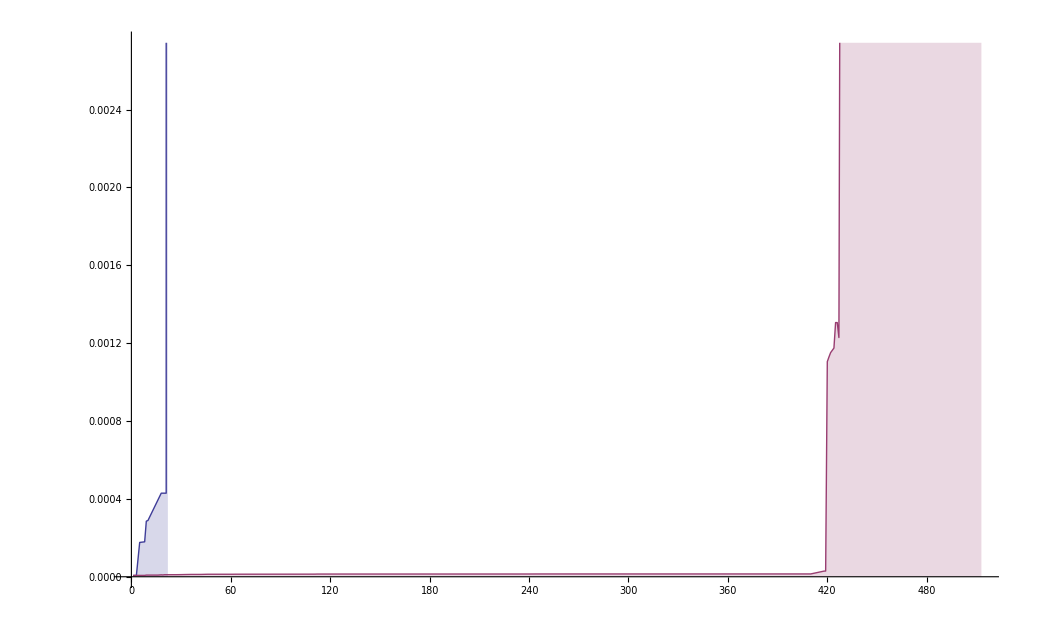

```mathematica
ListLinePlot[{evo1⟦All,{1,5}⟧,evo2⟦All,{1,5}⟧},Filling->Axis]
```

```mathematica
Times[Plus[1.8475257866594816 Times[Plus[1.1899364586157526 x1,1.1915446099656168 times[1]],times[1],x1,plus[0.45472407217122573 x0,-0.4557763400729498],1],0.9904494164983746 x1,0.13819415448068048,0.19604959992015275 atan[x0,x1]],1]/.{times->Times,plus->Plus,atan->ArcTan}
```

0.138194+0.990449 x1+1.84753 (-0.455776+0.454724 x0) x1 (1.19154+1.18994 x1)+0.19605 ArcTan[x0,x1]

```mathematica
Expand[plus[times[plus[x0,-1.],plus[x1,times[x1,x1]]],x1]/.{times->Times,plus->Plus,atan->ArcTan}]
```

0.+x0 x1-1. x1^2+x0 x1^2

```mathematica
Plot3D[{(0.13819415448068048+0.9904494164983746 x1+1.8475257866594816 (-0.4557763400729498+0.45472407217122573 x0) x1 (1.1915446099656168+1.1899364586157526 x1)+0.19604959992015275 ArcTan[x0,x1])-(x0*x1*x1+x0*x1-x1*x1)},{x0,-10,10},{x1,-10,10}]
```

-Graphics3D-